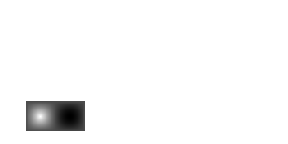

```mathematica
data = ({#[[3]],#[[2]],#[[1]]})&/@cardioidInPolarCoordinates;
peakValue = SortBy[data,(N[#[[3]]])&][[-1]];
(*
  For Some reason, My current implementation has 
has two values at the peak where r=1, and is
missing the value at the bottom of the valley 
where r = 0. I'll adjust it manually here
*)
If[Length[Position[data, peakValue]]>=2,
data[[Position[data,peakValue][[1]]]] = {peakValue[[1]]-Pi,peakValue[[2]],0}
];
sortedData = SortBy[data,{((N[#[[2]]])* 1000)+(N[#[[1]]] + 2Pi)&}];
(*
  We lost the x value for the first row of information.
It's Phi Angle did not survive the trip to cartesian 
 coordinates and back. We get the location back for
 Free when we partition the sorted data.
*)
matrixData = Partition[#[[3]]&/@sortedData,72];
ArrayPlot[matrixData,PixelConstrained->True,PlotRangePadding->None,Frame->None]
```

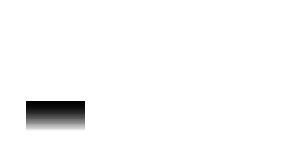

```mathematica
ArrayPlot[Table[(Cos[y*Pi/180/2]),{y,0 ,179,5},{x,0,359,5}],PixelConstrained->True,Frame->None,PlotRangePadding->None]
```

```mathematica
ListPointPlot3D[Part[sortedData,1;;1000],AspectRatio->Automatic, BoxRatios->{2, 1, 0.6},PlotRange->{{-Pi-0.5,Pi+0.5},{0-0.5,Pi+0.5}, {-0.5,1.5}}]
```

-Graphics3D-

```mathematica
Length[Position[sortedData, sortedData[[1]]]]
```

36

```mathematica
Dimensions[Table[(Cos[y*Pi/180/2]),{y,180 ,359,5},{x,0,359,5}]]
```

{36,72}

```mathematica
sphereData = ({#[[2]],#[[3]],#[[1]]})&/@sphereInSphericalCoordinates;
ListPointPlot3D[Part[sphereData,1;;2000],AspectRatio->Automatic, BoxRatios->{2, 1, 0.6},PlotRange->{{0-0.5,2*Pi+0.5},{0-0.5,Pi+0.5}, {-0.5,1.5}}]
```

-Graphics3D-